# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
<<LineCableParam2020`
```

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=10 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 138kV -- sem cabos pararraios

Coordenadas dos condutores

```mathematica
xc={-10,0,10};
yc={15,15,15};
```

Dados condutores de fase

```mathematica
rf=2.54*10^-2;
rint=8.03*10^-3;
Rdc=0.121*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-12,12},{5,30.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
ω= 2. π 60;
ρs= 1000.;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,rf,rint];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.180275+0.894448 ⅈ | 0.0586707+0.428199 ⅈ | 0.0586694+0.375937 ⅈ
0.0586707+0.428199 ⅈ | 0.180275+0.894448 ⅈ | 0.0586707+0.428199 ⅈ
0.0586694+0.375937 ⅈ | 0.0586707+0.428199 ⅈ | 0.180275+0.894448 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+3.05571×10^-6 ⅈ | 0.-4.68277×10^-7 ⅈ | 0.-1.78351×10^-7 ⅈ
0.-4.68277×10^-7 ⅈ | 3.×10^-9+3.11707×10^-6 ⅈ | 0.-4.68277×10^-7 ⅈ
0.-1.78351×10^-7 ⅈ | 0.-4.68277×10^-7 ⅈ | 3.×10^-9+3.05571×10^-6 ⅈ)

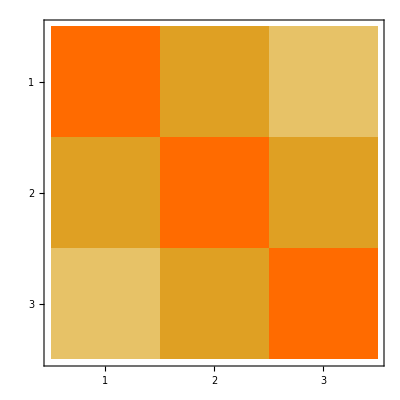

```mathematica
MatrixPlot[Abs@Zmat ]
```

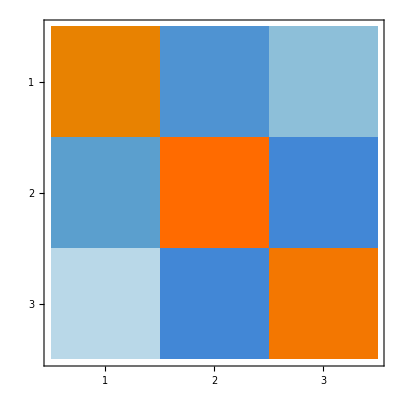

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
Zs = (Zmat[[1,1]]+Zmat[[2,2]]+Zmat[[3,3]])/3
```

0.000180275+0.000894448 ⅈ

```mathematica
Zm = (Zmat[[1,2]]+ Zmat[[1,3]]+Zmat[[2,3]])/3
```

0.0000586703+0.000410778 ⅈ

```mathematica
Zabc = Table[If[i!= j, Zm, Zs],{i,1,3},{j,1,3}];
MatrixForm[Zabc 1000]
```

(0.180275+0.894448 ⅈ | 0.0586703+0.410778 ⅈ | 0.0586703+0.410778 ⅈ
0.0586703+0.410778 ⅈ | 0.180275+0.894448 ⅈ | 0.0586703+0.410778 ⅈ
0.0586703+0.410778 ⅈ | 0.0586703+0.410778 ⅈ | 0.180275+0.894448 ⅈ)

```mathematica
Ys = (Ymat[[1,1]]+Ymat[[2,2]]+Ymat[[3,3]])/3
```

3.×10^-12+3.07617×10^-9 ⅈ

```mathematica
Ym = (Ymat[[1,2]]+ Ymat[[1,3]]+Ymat[[2,3]])/3
```

0.-3.71635×10^-10 ⅈ

```mathematica
Yabc = Table[If[i!= j, Ym, Ys],{i,1,3},{j,1,3}];
MatrixForm[Yabc 1000]
```

(3.×10^-9+3.07617×10^-6 ⅈ | 0.-3.71635×10^-7 ⅈ | 0.-3.71635×10^-7 ⅈ
0.-3.71635×10^-7 ⅈ | 3.×10^-9+3.07617×10^-6 ⅈ | 0.-3.71635×10^-7 ⅈ
0.-3.71635×10^-7 ⅈ | 0.-3.71635×10^-7 ⅈ | 3.×10^-9+3.07617×10^-6 ⅈ)

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012= Inverse[A].Zabc. A;
MatrixForm[Z012*1000]
```

(0.297616+1.716 ⅈ | -3.25261×10^-16-2.71051×10^-17 ⅈ | -2.71051×10^-16+0. ⅈ
1.0842×10^-16-1.0842×10^-16 ⅈ | 0.121605+0.483669 ⅈ | -2.71051×10^-17-4.06576×10^-17 ⅈ
1.0842×10^-16-1.0842×10^-16 ⅈ | 0.-2.71051×10^-17 ⅈ | 0.121605+0.483669 ⅈ)

```mathematica
MatrixForm[ 1000Inverse[A].Zmat.A]
```

(0.297616+1.716 ⅈ | 0.0150865-0.00871072 ⅈ | -0.015087-0.00870996 ⅈ
-0.015087-0.00870996 ⅈ | 0.121605+0.483669 ⅈ | -0.0301731+0.0174214 ⅈ
0.0150865-0.00871072 ⅈ | 0.0301739+0.0174199 ⅈ | 0.121605+0.483669 ⅈ)

```mathematica
Y012= Inverse[A].Yabc. A;
MatrixForm[Y012*1000]
```

(3.×10^-9+2.33289×10^-6 ⅈ | 1.03398×10^-22+0. ⅈ | 1.03398×10^-22+0. ⅈ
0.+2.06795×10^-22 ⅈ | 3.×10^-9+3.4478×10^-6 ⅈ | 0.+0. ⅈ
0.+1.03398×10^-22 ⅈ | 0.+0. ⅈ | 3.×10^-9+3.4478×10^-6 ⅈ)

```mathematica
Z0= Z012[[1,1]]*1000
```

0.297616+1.716 ⅈ

```mathematica
Zpos= Z012[[2,2]]*1000
```

0.121605+0.483669 ⅈ

```mathematica
Ypos=Y012[[2,2]]*1000
```

3.×10^-9+3.4478×10^-6 ⅈ

```mathematica
Zc= Sqrt[Zpos/Ypos]
```

377.467-46.5578 ⅈ

```mathematica
Pn = 138^2/Zc
```

49.696+6.12963 ⅈ

```mathematica
ℓ= 80.0;
Y1= 1/(Zpos ℓ) + Ypos ℓ;
Y2= -1/(Zpos ℓ);
 ZL= 376.32086209393407;
Y3= 1/ZL;
```

```mathematica
Yn={{Y1, Y2},{Y2, Y1+ Y3}};
MatrixForm@Yn
```

(0.00613517-0.0240298 ⅈ | -0.00613493+0.0243072 ⅈ
-0.00613493+0.0243072 ⅈ | 0.00879248-0.0240298 ⅈ)

```mathematica
Zn= Inverse[Yn];
MatrixForm@Zn
```

(377.679-40.1974 ⅈ | 363.975-77.4162 ⅈ
363.975-77.4162 ⅈ | 360.281-75.5967 ⅈ)

```mathematica
Vn=138./Sqrt[3]
```

79.6743

```mathematica
I1= Vn/Zn[[1,1]]1000
```

208.595+22.2013 ⅈ

```mathematica
V2=Zn[[2,1]] I1
```

77642.1-8067.9 ⅈ

```mathematica
V2 Sqrt[3]
```

134480.-13974. ⅈ

```mathematica
Arg[V2]/Degree
```

-5.93239

```mathematica
Abs[V2/(138 10^3/Sqrt[3])]
```

0.97974

```mathematica
IL= V2/ ZL
```

206.319-21.4389 ⅈ

```mathematica
3 10^-3 V2 Conjugate[IL]
```

48576.+0. ⅈ

```mathematica
V2a= 138 /Sqrt[3];
I2a= V2a/ZL;
```

```mathematica
a =1+ (Zpos ℓ) Ypos ℓ;
b =(Zpos ℓ);
c= A Ypos ℓ+  Ypos ℓ;
```

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.989273+0.0027173 ⅈ | 9.76157+38.6763 ⅈ
-2.76396×10^-7+0.000551857 ⅈ | 0.989273+0.0027173 ⅈ)

```mathematica
sol=Q.{V2a, I2a}
```

{80.8864+8.40501 ⅈ,0.209426+0.0445441 ⅈ}

```mathematica
sol[[1]] Sqrt[3]/138
```

1.01521+0.105492 ⅈ

```mathematica
Arg[sol[[1]]]/Degree
```

5.93239

```mathematica
Q1={{1, (Zpos ℓ)},{0,1}};
MatrixForm[Q1]
```

(1 | 9.76157+38.6763 ⅈ
0 | 1)

```mathematica
sol1=Q1.{V2a, I2a}
```

{81.741+8.18851 ⅈ,0.211719+0. ⅈ}

```mathematica
Arg[sol1[[1]]]/Degree
```

5.72059